```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
```

```mathematica
Figure 3a: Initial Wildtype sensitivity
```

```mathematica
nStart=1;
nEnd=60;
nFiles = nEnd-nStart+1;
date="2020-09-10";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n,Break[]],{n,1,100}]*)
WTSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nFiles];
(*Tf=700;
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["SolarColors"][#]]}}&/@Range[0,1,1/nFiles];
fig3a=ListPlot[
Table[{#,WTSurvivalCurves[[l]][#]}&/@Range[0,Tf,10],{l,1,nFiles}],
Joined->True,
PlotRange->{{-0.01,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[{"0.05","0.10","0.15","0.2"},{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]*)
```

```mathematica
tumorLegend=ToString@@@{min,25,median,75,max};
```

```mathematica
WTinit=#&/@Range[12];
```

```mathematica
WTlongterm=ArrayReshape[#[720]&/@WTSurvivalCurves,{5,12}]
(*WTplotdata=Transpose@{WTinit,WTlongterm};*)
```

{{1,0.996,0.991,0.954,0.851,0.688,0.497,0.346,0.194,0.119,0.045,0.025},{1,0.997,0.945,0.872,0.743,0.541,0.366,0.182,0.089,0.04,0.025,0.011},{0.998,0.976,0.92,0.787,0.624,0.426,0.259,0.125,0.076,0.035,0.014,0.009},{0.989,0.948,0.878,0.679,0.517,0.324,0.176,0.101,0.047,0.014,0.009,0.001},{0.985,0.93,0.82,0.617,0.443,0.271,0.134,0.073,0.028,0.009,0.005,0.002}}

```mathematica
WTplotdata=Transpose@{WTinit,WTlongterm[[#]]}&/@Range[5];
```

```mathematica
L2[SurvivalCurve_,c_,i_]:=ListLogPlot[SurvivalCurve,
PlotRange->{{0.5,12.5},{0.00005,2.075}},
PlotStyle->Directive[c,PointSize->0.025],
PlotLegends->Placed[SwatchLegend[{tumorLegend[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],{0.15,0.4}],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.325
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
,FrameLabel->{"Normal T cells/µL at infusion","Probability of CR"}
];
```

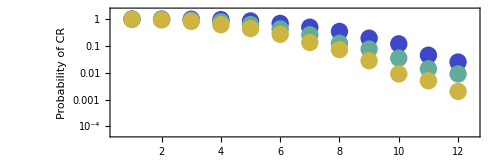

```mathematica
Show[L2[WTplotdata[[1]],ColorData["Rainbow"][0.15],1],L2[WTplotdata[[3]],ColorData["Rainbow"][0.4],3],L2[WTplotdata[[5]],ColorData["Rainbow"][0.7],5]]
```

```mathematica
Export[NotebookDirectory[]<>"varyingSigma.pdf",fig3a,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingSigma.pdf

### Histogram of cure and progression

```mathematica
getCureProgression[num_]:=Module[
{a,cure,progression},
a=makeSurvivalCurve["outputData_"<>ToString[num]<>"_"<>date<>".txt"][[1]];
cure={};
progression={};
If[a[[#]]>10000,AppendTo[cure,a[[#]]-10000],AppendTo[progression,a[[#]]]]&/@Range[1,Length[a]];
{cure,progression}
];
```

0.277

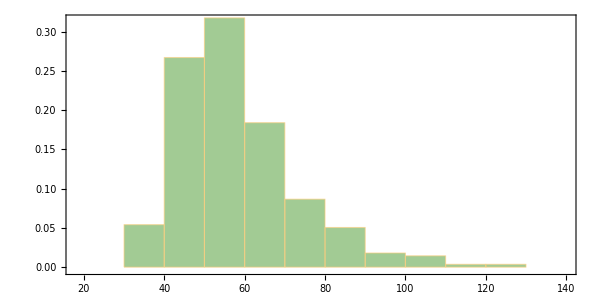

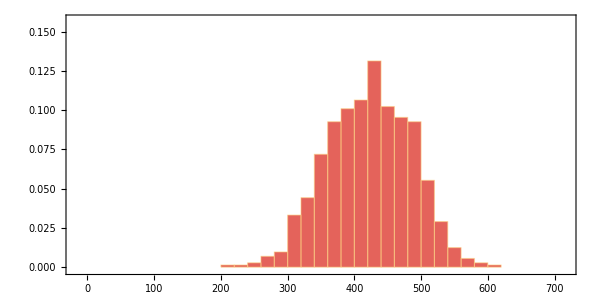

```mathematica
(* This module creates a K-M curve using the given filename *)
date="2020-09-09";
{cure,progression}=getCureProgression[5];
options={
Frame->{{True,False},{True,False}}
,LabelStyle->{FontSize->18,FontFamily->"Arial"}
,AspectRatio->0.5
,ImageSize->600
,FrameTicks->{{All,None},{All,None}}
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
};
Tf=700;
Length[cure]/1000//N
histCure=Histogram[
cure,"Scott","Probability",ChartStyle->{Opacity[0.75,ColorData["Rainbow"][0.5]]}
,options
,PlotRange->{{18,140},{-0.01,1.05}0.3}
]
histProg=Histogram[
progression,"Scott","Probability",ChartStyle->{Opacity[0.75,ColorData["Rainbow"][0.98]]}
,options
,PlotRange->{{-0.025,1.025}Tf,{-0.01,1.05}0.15}
]
```

```mathematica
Export[NotebookDirectory[]<>"histCure.pdf",histCure,"PDF"]
Export[NotebookDirectory[]<>"histProgression.pdf",histProg,"PDF"]
```

```mathematica
Figure 3b: tumor growth rate sensitivity
```

```mathematica
nStart=61;
nEnd=85;
nFiles = nEnd-nStart+1;
date="2020-09-10";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n,Break[]],{n,1,100}]*)
rBSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

```mathematica
rBSurvivalCurves[[-1]][1000]
```

0.998

```mathematica
tumorLegend=ToString@@@{min,25,median,75,max};
```

```mathematica
rBvec=0.025(#-1)+0.04&/@Range[5];
```

```mathematica
rBlongterm=ArrayReshape[#[720]&/@rBSurvivalCurves,{5,5}]
(*WTplotdata=Transpose@{WTinit,WTlongterm};*)
```

{{0.814,0.703,0.616,0.47,0.361},{0.689,0.546,0.428,0.31,0.202},{0.599,0.403,0.29,0.219,0.152},{0.566,0.332,0.223,0.151,0.107},{0.577,0.274,0.164,0.095,0.07}}

```mathematica
rBplotdata=Transpose@{rBvec,rBlongterm[[#]]}&/@Range[5];
```

```mathematica
L3[SurvivalCurve_,c_,i_,xlabel_]:=ListPlot[SurvivalCurve,
PlotRange->{{0.035,0.145},{-0.05,1.05}},
PlotStyle->Directive[c,PointSize->0.025],
PlotLegends->Placed[SwatchLegend[{tumorLegend[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],Top],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.325
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
,FrameLabel->{xlabel,"Probability of CR"}
];
```

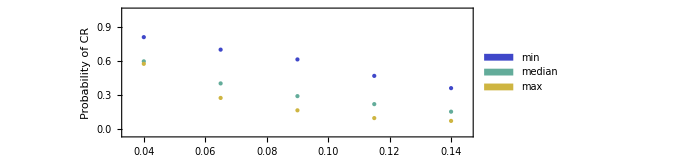

```mathematica
Show[L3[rBplotdata[[1]],ColorData["Rainbow"][0.15],1,"Tumor growth rate"],L3[rBplotdata[[3]],ColorData["Rainbow"][0.4],3,"Tumor growth rate"],L3[rBplotdata[[5]],ColorData["Rainbow"][0.7],5,"Tumor growth rate"]]
```

```mathematica
Figure 3c: kC sensitivity
```

```mathematica
nStart=86;
nEnd=140;
nFiles = nEnd-nStart+1;
date="2020-09-10";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n,Break[]],{n,1,100}]*)
kCSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

```mathematica
kCSurvivalCurves[[3]][1000]
```

0

```mathematica
tumorLegend=ToString@@@{min,25,median,75,max};
```

```mathematica
kCvec=10(#-1)+100&/@Range[11];
```

```mathematica
kClongterm=ArrayReshape[#[720]&/@kCSurvivalCurves,{5,11}]
(*WTplotdata=Transpose@{WTinit,WTlongterm};*)
```

{{0,0.002,0.059,0.313,0.73,0.948,0.987,1,1,1,1},{0,0,0.015,0.186,0.561,0.873,0.981,0.998,1,1,1},{0,0,0.006,0.11,0.476,0.808,0.975,0.998,0.998,1,1},{0,0,0.001,0.084,0.39,0.738,0.94,0.991,0.999,1,1},{0,0,0.002,0.055,0.274,0.708,0.928,0.985,0.997,1,1}}

```mathematica
kCplotdata=Transpose@{kCvec,kClongterm[[#]]}&/@Range[5]
```

{{{100,0},{110,0.002},{120,0.059},{130,0.313},{140,0.73},{150,0.948},{160,0.987},{170,1},{180,1},{190,1},{200,1}},{{100,0},{110,0},{120,0.015},{130,0.186},{140,0.561},{150,0.873},{160,0.981},{170,0.998},{180,1},{190,1},{200,1}},{{100,0},{110,0},{120,0.006},{130,0.11},{140,0.476},{150,0.808},{160,0.975},{170,0.998},{180,0.998},{190,1},{200,1}},{{100,0},{110,0},{120,0.001},{130,0.084},{140,0.39},{150,0.738},{160,0.94},{170,0.991},{180,0.999},{190,1},{200,1}},{{100,0},{110,0},{120,0.002},{130,0.055},{140,0.274},{150,0.708},{160,0.928},{170,0.985},{180,0.997},{190,1},{200,1}}}

```mathematica
L3[SurvivalCurve_,c_,i_,xlabel_]:=ListPlot[SurvivalCurve,
PlotRange->{{95,205},{-0.1,1.1}},
PlotStyle->Directive[c,PointSize->0.025],
PlotLegends->Placed[SwatchLegend[{tumorLegend[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],Top],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.325
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
,FrameLabel->{xlabel,"Probability of CR"}
];
```

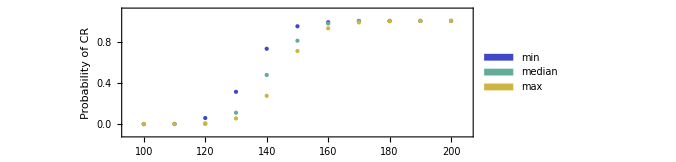

```mathematica
Show[L3[kCplotdata[[1]],ColorData["Rainbow"][0.15],1,"CAR T carrying capacity"],L3[kCplotdata[[3]],ColorData["Rainbow"][0.4],3,"CAR T carrying capacity"],L3[kCplotdata[[5]],ColorData["Rainbow"][0.7],5,"CAR T carrying capacity"]]
```

```mathematica
death=Flatten[Import[dir<>"ZUMA1_PFS_death.dat"],0];
L=death//Length;
avMonth=(7 31+28+4*30)/12.;
e=Join[{{0,1}},{death⟦#,1⟧avMonth,death⟦#,2⟧1./100.}&/@Range[1,L,1]];

nStart=141;
nEnd=210;
nFiles = nEnd-nStart+1
date="2020-09-10";

Tf=400;
plotShow[num_,curve_,val_]:=LPsim=ListPlot[(*{rB1[x],rB2[x],rB3[x]},{x,0,Tf},*)
{
e,
{#,curve[[num]][#]}&/@Range[0,1.05Tf,Tf/1000.]
},
Joined->{True,True},
PlotRange->{{-0.01,1.05}Tf ,{-0.05,1.025}},
PlotLegends->Placed[{"",""},{0.45,0.85}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500,
AspectRatio->0.35
,PlotStyle->{
{Thickness[0.0075],Opacity[0.5,Black]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][val]}
}
]
rBsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

70

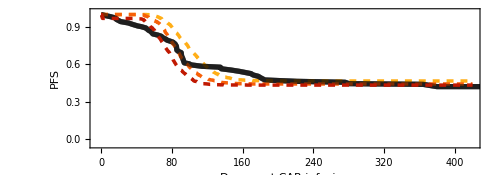

```mathematica
Show[plotShow[40,rBsurvivalCurves,0.8],plotShow[47,rBsurvivalCurves,0.5],plotShow[69,rBsurvivalCurves,0.2]]
```

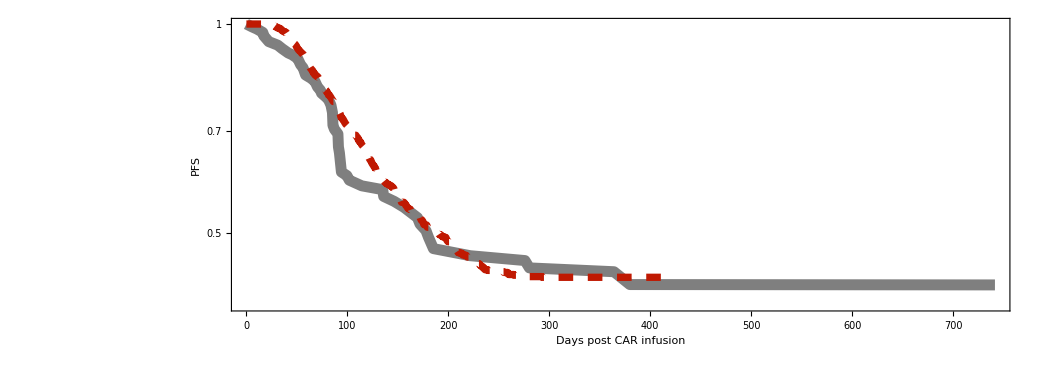

```mathematica
plotShowLog[num_,curve_]:=LPsim=ListLogPlot[(*{rB1[x],rB2[x],rB3[x]},{x,0,Tf},*)
{
e,
{#,curve[[num]][#]}&/@Range[0,1.05Tf,Tf/1000.]
},
Joined->{True,True},
(*PlotRange->{{-0.01,1.05}Tf ,{-0.05,1.025}},*)
PlotLegends->Placed[{"",""},{0.45,0.85}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500,
AspectRatio->0.35
,PlotStyle->{
{Thickness[0.0075],Opacity[0.5,Black]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.2]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.6]}
}
]

plotShowLog[6,rBsurvivalCurves]
```

```mathematica
tumorSizes={4.24,
9.21,
23.84,
37.33,
58.27,
94.62,
132.83,
162.2,
169.56,
170.31,
182.51,
210.34,
225.13,
226.52,
290.78,
324.47,
535.53,
411.44,
499.6,
536.3,
619.2,
659.4};
```

```mathematica
date="2020-09-08";
cureRate[num_]:=Module[
{a,cure,progression},
a=makeSurvivalCurve["outputData_"<>ToString[num]<>"_"<>date<>".txt"][[1]];
cure={};
progression={};
If[a[[#]]>10000,AppendTo[cure,a[[#]]-10000],AppendTo[progression,a[[#]]]]&/@Range[1,Length[a]];
Length[cure]/1000//N
];
```

```mathematica
lightToDark[n_,c_:Red,reverse_:False]:=Blend[{{0,White},{n/2,c},{n+3,Black}},If[reverse,n-#+1,#]]&/@Range[n];
```

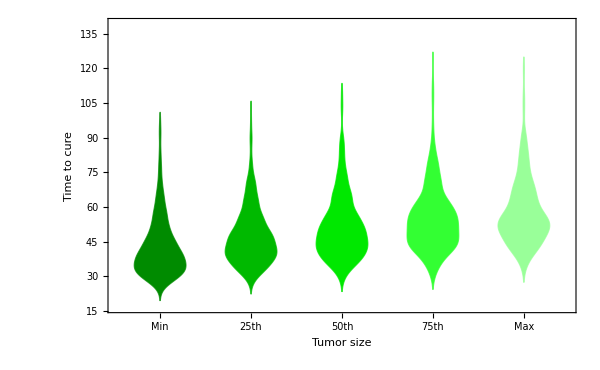

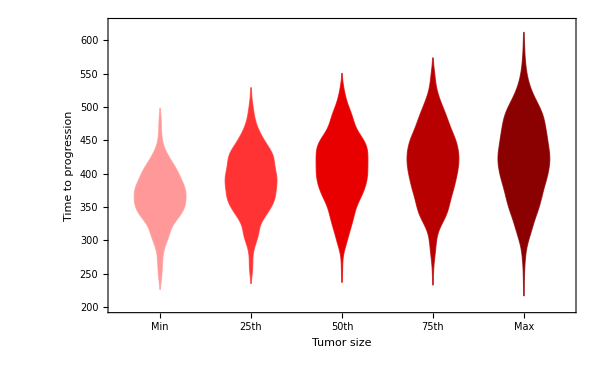

```mathematica
DistributionChart[getCureProgression[#][[1]]&/@Range[5],ChartStyle->lightToDark[5,Green,True],ChartLabels->{"Min","25th","50th","75th","Max"},
FrameLabel->{"Tumor size","Time to cure"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600]
DistributionChart[getCureProgression[#][[2]]&/@Range[5],ChartStyle->lightToDark[5],ChartLabels->{"Min","25th","50th","75th","Max"},
FrameLabel->{"Tumor size","Time to progression"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600]
```

```mathematica
data={tumorSizes[[#]],cureRate[#+22]}&/@Range[22]
```

{{4.24,0.663},{9.21,0.608},{23.84,0.524},{37.33,0.51},{58.27,0.472},{94.62,0.403},{132.83,0.392},{162.2,0.41},{169.56,0.409},{170.31,0.412},{182.51,0.353},{210.34,0.391},{225.13,0.348},{226.52,0.377},{290.78,0.339},{324.47,0.325},{535.53,0.287},{411.44,0.32},{499.6,0.295},{536.3,0.305},{619.2,0.297},{659.4,0.302}}

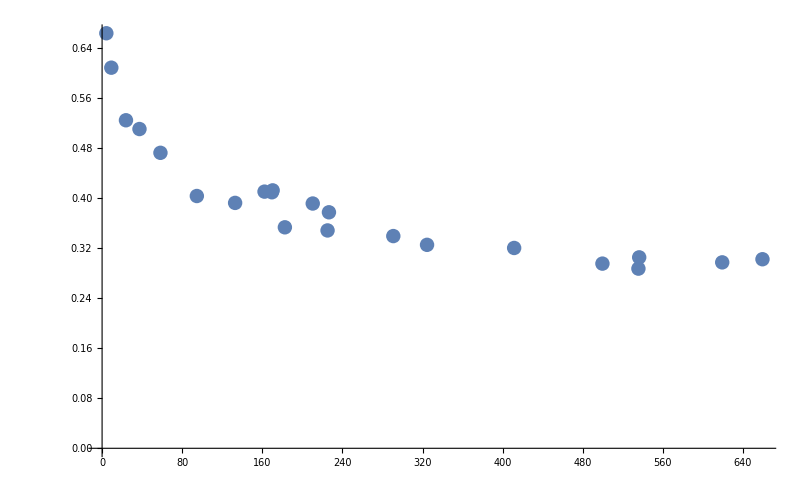

```mathematica
ListPlot[data]
```

```mathematica
Median[tumorSizes]
```

196.425

```mathematica
Median[data[[1;;11,2]]]
```

0.412

```mathematica
data[[;;,2]]
```

{0.663,0.608,0.524,0.51,0.472,0.403,0.392,0.41,0.409,0.412,0.353,0.391,0.348,0.377,0.339,0.325,0.287,0.32,0.295,0.305,0.297,0.302}

```mathematica
ArrayReshape[Table[i,{i,60}],{5,12}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,16,17,18,19,20,21,22,23,24},{25,26,27,28,29,30,31,32,33,34,35,36},{37,38,39,40,41,42,43,44,45,46,47,48},{49,50,51,52,53,54,55,56,57,58,59,60}}